{{100,0,0,0,0,0,0,0,0,0,0,0},{32,68,0,0,0,0,0,0,0,0,0,0},{17,33,50,0,0,0,0,0,0,0,0,0},{12,20,35,33,0,0,0,0,0,0,0,0},{9,17,20,24,30,0,0,0,0,0,0,0},{9,9,15,18,22,27,0,0,0,0,0,0},{8,8,14,13,18,17,22,0,0,0,0,0},{8,5,9,11,15,20,15,17,0,0,0,0},{6,4,7,13,9,11,19,17,14,0,0,0},{5,3,7,10,7,13,11,13,19,12,0,0},{5,3,6,6,11,6,10,16,7,19,11,0},{4,3,5,5,11,4,12,6,17,5,18,10}}

{9,17,20,24,30,0,0,0,0,0,0,0}

(100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
32 | 68 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17 | 33 | 50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12 | 20 | 35 | 33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 17 | 20 | 24 | 30 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 9 | 15 | 18 | 22 | 27 | 0 | 0 | 0 | 0 | 0 | 0
8 | 8 | 14 | 13 | 18 | 17 | 22 | 0 | 0 | 0 | 0 | 0
8 | 5 | 9 | 11 | 15 | 20 | 15 | 17 | 0 | 0 | 0 | 0
6 | 4 | 7 | 13 | 9 | 11 | 19 | 17 | 14 | 0 | 0 | 0
5 | 3 | 7 | 10 | 7 | 13 | 11 | 13 | 19 | 12 | 0 | 0
5 | 3 | 6 | 6 | 11 | 6 | 10 | 16 | 7 | 19 | 11 | 0
4 | 3 | 5 | 5 | 11 | 4 | 12 | 6 | 17 | 5 | 18 | 10)

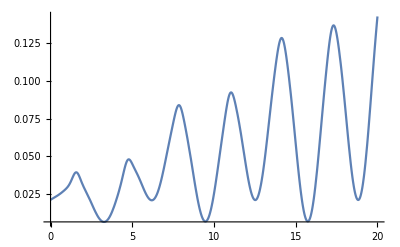

```mathematica
T=RandomInteger[{1,20}];
lim = 5;
stake =100;
f[x_] = (x*Sin[x]^2+D[Cos[x],{x,T}]+D[Sin[x],{x,T}]+Sin[x]^T+2);
F[x_] = f[t]/NIntegrate[f[t],{t,0,T}];
S = Table[Table[Round[stake*NIntegrate[F[t],{t,i*T/rounds,(i+1)*T/rounds}]],{i,0,rounds-1}],{rounds,1,12,1}];

padS = Table[PadRight[Part[S,i],12],{i,1,12}];
check=Table[Sum[Part[padS,i,j],{j,1,Length[Part[S,i]]}],{i,1,12}];

For[p=1,p<13,p++,padS[[p,1]]+=(100-check[[p]])];
padS
padS[[lim]]
MatrixForm[padS]
newCheck=Table[Sum[Part[padS,i,j],{j,1,Length[Part[S,i]]}],{i,1,12}];

F[x];
Plot[F[t],{t,0,T},PlotRange->Full ]
DiscretePlot[F[t],{t,0,T, T/(12-1)},ExtentSize->Full,ExtentMarkers->None];
```